```mathematica
SetDirectory[NotebookDirectory[]]
Get["deficiency.wl"]
```

/home/felix/downloads/submit-repo

This notebooks demonstrates the algorithm implemented in deficiency.wl. The most important functions are:
* QuickDeficiencyIndices[poly_]: Returns the deficiency indices of poly_
* AdaptiveDeficiencyIndices[poly_]: The implementation of QuickDeficiencyIndices, displaying all the metadata and error codes
* DeficiencyPlot[poly_,z_,n_]: Returns the first n radia, ready to be plotted with list plot

We start by applying the algorithm on operators with known analytical results, then apply it onto operators from the literature, reproducing the table in the paper.
We proceed to sweep over parameters of an operator, reproducing the phase plot from the paper, and end with an exemplary plot of the radii.

# Operators with known analytical results

## Gaussian and Diagonal Operations

```mathematica
QuickDeficiencyIndices[a+adag]
```

H = a^†+a
n_+ = 0,   n_- = 0   —   good Hamiltonian

```mathematica
QuickDeficiencyIndices[a**a+adag**adag]
```

H = (a^†)^2+a^2
n_+ = 0,   n_- = 0   —   good Hamiltonian

```mathematica
QuickDeficiencyIndices[p**p-x**x]
```

H = p^2-x^2
n_+ = 0,   n_- = 0   —   good Hamiltonian

## Higher Order Squeezing

```mathematica
QuickDeficiencyIndices[a**a**a+adag**adag**adag]
```

H = (a^†)^3+a^3
n_+ = 3,   n_- = 3   —   more physical information necessary

```mathematica
QuickDeficiencyIndices[a**a**a**a+adag**adag**adag**adag]
```

H = (a^†)^4+a^4
n_+ = 4,   n_- = 4   —   more physical information necessary

```mathematica
QuickDeficiencyIndices[adag**adag**a+adag**a**a]
```

H = (a^†)^2 a+a^†a^2
n_+ = 1,   n_- = 1   —   more physical information necessary

```mathematica
QuickDeficiencyIndices[a**a**a**a+adag**adag**adag**adag+adag**a**adag**a]
```

H = (a^†)^4+a^†a a^†a+a^4
n_+ = 4,   n_- = 4   —   more physical information necessary

```mathematica
QuickDeficiencyIndices[a**a**a**a+adag**adag**adag**adag+3adag**a**adag**a]
```

H = (a^†)^4+3 (a^†a a^†a)+a^4
n_+ = 0,   n_- = 0   —   good Hamiltonian

```mathematica
QuickDeficiencyIndices[adag**adag**a+adag**a**a]
```

H = (a^†)^2 a+a^†a^2
n_+ = 1,   n_- = 1   —   more physical information necessary

## Schrödinger Operators

```mathematica
QuickDeficiencyIndices[p**p+x**x**x]
```

H = p^2+x^3
n_+ = 1,   n_- = 1   —   more physical information necessary

```mathematica
QuickDeficiencyIndices[p**p+x**x**x**x]
```

H = p^2+x^4
n_+ = 0,   n_- = 0   —   good Hamiltonian

```mathematica
QuickDeficiencyIndices[p**p-x**x**x**x]
```

H = p^2-x^4
n_+ = 2,   n_- = 2   —   more physical information necessary

## Operators without self-adjoint extensions

```mathematica
QuickDeficiencyIndices[p**p**p**x+x**p**p**p]
```

H = p^3 x+x p^3
n_+ = 2,   n_- = 0   —   bad Hamiltonian

```mathematica
QuickDeficiencyIndices[x**x**x**p+p**x**x**x]
```

H = p x^3+x^3 p
n_+ = 0,   n_- = 2   —   bad Hamiltonian

# Operators from the Literature

## Cubic Phase Gate

```mathematica
QuickDeficiencyIndices[x**x**x]
```

H = x^3
n_+ = 0,   n_- = 0   —   good Hamiltonian

## Kerr nonlinearities, appearing throughout the literature

```mathematica
QuickDeficiencyIndices[adag**adag+a**a+adag**adag**a**a]
```

H = (a^†)^2+a^2+(a^†)^2 a^2
n_+ = 0,   n_- = 0   —   good Hamiltonian

```mathematica
QuickDeficiencyIndices[adag**adag+a**a+adag**adag**a**a+adag**adag**a+adag**a**a]
```

H = (a^†)^2+(a^†)^2 a+a^2+a^†a^2+(a^†)^2 a^2
n_+ = 0,   n_- = 0   —   good Hamiltonian

```mathematica
QuickDeficiencyIndices[adag**adag**a**a+adag**a+Hermitianify[a+a**a+adag**a**a]]
```

H = 1/2 (NonCommutativeMultiply(a^†)2**+a^†NonCommutativeMultiplya2**+NonCommutativeMultiply(a^†)2**a+a^†+NonCommutativeMultiplya2**+a)+a^†a+(a^†)^2 a^2
n_+ = 0,   n_- = 0   —   good Hamiltonian

#### Self-adjointness can depend on parameters

```mathematica
QuickDeficiencyIndices[adag**adag**a**a-(adag**a**a**a+adag**adag**adag**a)-10(adag**adag**adag**adag+a**a**a**a)]
```

H = -(a^†)^3 a-10 ((a^†)^4+a^4)-a^†a^3+(a^†)^2 a^2
n_+ = 4,   n_- = 4   —   more physical information necessary

```mathematica
QuickDeficiencyIndices[adag**adag**a**a-(adag**a**a**a+adag**adag**adag**a)-1/10(adag**adag**adag**adag+a**a**a**a)]
```

H = -(a^†)^3 a+1/10 (-(a^†)^4-a^4)-a^†a^3+(a^†)^2 a^2
n_+ = 2,   n_- = 2   —   more physical information necessary

```mathematica
QuickDeficiencyIndices[adag**adag**a**a-1/10(adag**a**a**a+adag**adag**adag**a)-1/10(adag**adag**adag**adag+a**a**a**a)]
```

H = 1/10 (-(a^†)^4-a^4)+1/10 (-(a^†)^3 a-(a^†a^3))+(a^†)^2 a^2
n_+ = 0,   n_- = 0   —   good Hamiltonian

## Phase nonlinearities, appearing throughout the literature

```mathematica
QuickDeficiencyIndices[adag**a +x+x**x+ GeneralizedPower[NonCommutativeMultiply,x,4]]
```

H = a^†a+NonCommutativeMultiplyx4**+x^2+x
n_+ = 0,   n_- = 0   —   good Hamiltonian

```mathematica
QuickDeficiencyIndices[adag**a +x+x**x- GeneralizedPower[NonCommutativeMultiply,x,4]]
```

H = a^†a-NonCommutativeMultiplyx4**+x^2+x
n_+ = 2,   n_- = 2   —   more physical information necessary

## S. Lloyd and S. L. Braunstein, Quantum Computation over Continuous Variables, Phys. Rev. Lett. 82, 1784 (1999)

```mathematica
LBH = (p**p + x**x)/2;
LBH2 = GeneralizedPower[NonCommutativeMultiply,LBH,2];
LBS = x**p+ p**x;
```

```mathematica
QuickDeficiencyIndices[ⅈ Commutator[LBH2,x]]
```

H = ⅈ (NonCommutativeMultiply(1/2 (p**p+x**x))2**x-xNonCommutativeMultiply(1/2 (p**p+x**x))2**)
n_+ = 1,   n_- = 1   —   more physical information necessary

```mathematica
QuickDeficiencyIndices[ⅈ Commutator[LBH2,p]]
```

H = ⅈ (NonCommutativeMultiply(1/2 (p**p+x**x))2**p-pNonCommutativeMultiply(1/2 (p**p+x**x))2**)
n_+ = 1,   n_- = 1   —   more physical information necessary

```mathematica
QuickDeficiencyIndices[ⅈ Commutator[LBH2,LBS]]
```

H = ⅈ (NonCommutativeMultiply(1/2 (p**p+x**x))2**p**x+x**p-p**x+x**pNonCommutativeMultiply(1/2 (p**p+x**x))2**)
n_+ = 2,   n_- = 2   —   more physical information necessary

```mathematica
QuickDeficiencyIndices[Commutator[x,Commutator[LBH2,LBS]]]
```

H = xNonCommutativeMultiply(1/2 (p**p+x**x))2****(p**x+x**p)-(p**x+x**p)**NonCommutativeMultiply(1/2 (p**p+x**x))2**-NonCommutativeMultiply(1/2 (p**p+x**x))2****(p**x+x**p)-(p**x+x**p)**NonCommutativeMultiply(1/2 (p**p+x**x))2**x
n_+ = 0,   n_- = 0   —   good Hamiltonian

```mathematica
QuickDeficiencyIndices[Commutator[p,Commutator[LBH2,LBS]]]
```

H = pNonCommutativeMultiply(1/2 (p**p+x**x))2****(p**x+x**p)-(p**x+x**p)**NonCommutativeMultiply(1/2 (p**p+x**x))2**-NonCommutativeMultiply(1/2 (p**p+x**x))2****(p**x+x**p)-(p**x+x**p)**NonCommutativeMultiply(1/2 (p**p+x**x))2**p
n_+ = 0,   n_- = 0   —   good Hamiltonian

## R. Gordillo-Hachuel, E. Torrontegui, C. de Dios, and R. Puebla, Quantum metrological advantage of high-order squeezed states (2026), arXiv:2604.09958 [quant-ph]. J. Guo, S. Liu, B. Jing, Q. He, and M. Gessner, Metrological Sensitivity beyond Gaussian Limits with Cubic Phase States (2025), arXiv:2512.03769 [quant-ph]

```mathematica
QuickDeficiencyIndices[x**x**p+x**p**x+p**x**x]
```

H = p x^2+x^2 p+xpx
n_+ = 1,   n_- = 1   —   more physical information necessary

```mathematica
QuickDeficiencyIndices[x**p**p+p**x**p+p**p**x]
```

H = p^2 x+x p^2+pxp
n_+ = 1,   n_- = 1   —   more physical information necessary

```mathematica
QuickDeficiencyIndices[x**x**x**p+x**x**p**x+x**p**x**x+p**x**x**x]
```

H = p x^3+x^3 p+xp x^2+x^2 px
n_+ = 0,   n_- = 2   —   bad Hamiltonian

```mathematica
QuickDeficiencyIndices[x**x**p**p+x**p**x**p+x**p**p**x+p**x**x**p+p**x**p**x+p**p**x**x]
```

H = p^2 x^2+x^2 p^2+x p^2 x+p x^2 p+pxpx+xpxp
n_+ = 4,   n_- = 4   —   more physical information necessary

```mathematica
QuickDeficiencyIndices[x**p**p**p+p**x**p**p+p**p**x**p+p**p**p**x]
```

H = p^3 x+x p^3+px p^2+p^2 xp
n_+ = 2,   n_- = 0   —   bad Hamiltonian

## S. Kwon, D. Hoshi, T. Nagase, D. Sugiyama, H. Mukai, K. Takemura, R. Kojima, Y. Zhou, S. Watabe, F. Yoshihara, and J.-S. Tsai, Realisation of a Protected Cat Qutrit Manifold via Engineered Quantum Tunnelling (2026),arXiv:2601.17675 [quant-ph]

```mathematica
QuickDeficiencyIndices[adag**a+adag**adag**a**a+Hermitianify[a**a**a+adag**a**a**a**a]]
```

H = 1/2 (NonCommutativeMultiply(a^†)3**+a^†NonCommutativeMultiplya4**+NonCommutativeMultiply(a^†)4**a+NonCommutativeMultiplya3**)+a^†a+(a^†)^2 a^2
n_+ = 3,   n_- = 3   —   more physical information necessary

## A. Kasri, K. Park, and R. Filip, Nonlinear Phase Gates Beyond the Lamb-Dicke Regime (2026), arXiv:2602.15619 [quant-ph]

```mathematica
QuickDeficiencyIndices[ⅈ(η (adag-a)+η^3/2(adag**adag**a-adag**a**a))/.{η->1/10}]
```

H = ⅈ (1/10 (a^†-a)+((a^†)^2 a-a^†a^2)/2000)
n_+ = 1,   n_- = 1   —   more physical information necessary

Some  parameter regimes make the numerical analysis significantly harder, but are analytically known to have the same result

```mathematica
QuickDeficiencyIndices[ⅈ(η (adag-a)+η^3/2(adag**adag**a-adag**a**a))/.{η->10}]
```

H = ⅈ (10 (a^†-a)+500 ((a^†)^2 a-a^†a^2))
Error: Failed to compute deficiency indices. Use AdapativeDeficiencyIndices for detailed output and ListPlot@DeficiencyIndices for visual feedback
Possible Problems: MaxAlgorithm Length is not sufficient; ϵ_1 is too large

```mathematica
QuickDeficiencyIndices[(η^2 (adag**adag+a**a)-η^4/4!(adag**adag**adag**a+adag**a**a**a))/.{η->1}]
```

H = (a^†)^2+a^2+1/24 (-(a^†)^3 a-(a^†a^3))
n_+ = 2,   n_- = 2   —   more physical information necessary

```mathematica
QuickDeficiencyIndices[(η^2 (adag**adag+a**a)-η^4/4!(adag**adag**adag**a+adag**a**a**a))/.{η->1/10}]
```

H = (-(a^†)^3 a-(a^†a^3))/240000+1/100 ((a^†)^2+a^2)
Error: Failed to compute deficiency indices. Use AdapativeDeficiencyIndices for detailed output and ListPlot@DeficiencyIndices for visual feedback
Possible Problems: MaxAlgorithm Length is not sufficient; ϵ_1 is too large

```mathematica
QuickDeficiencyIndices[(η^2 (adag**adag+a**a)-η^4/4!(adag**adag**adag**a+adag**a**a**a))/.{η->1}]
```

H = (a^†)^2+a^2+1/24 (-(a^†)^3 a-(a^†a^3))
n_+ = 2,   n_- = 2   —   more physical information necessary

# Phase diagrams of deficiency indices

## S. Boutin, D. M. Toyli, A. V. Venkatramani, A. W. Eddins, I. Siddiqi, and A. Blais, Effect of Higher-Order Nonlinearities on Amplification and Squeezing in Josephson Parametric Amplifiers, Phys. Rev. Appl. 8, 054030 (2017).

```mathematica
Hparam = adag**adag**adag**adag + c1 adag**adag**adag**a+c2 adag**adag**a**a + c1 adag**a**a**a + a**a**a**a
```

a**a**a**a+c1 adag**a**a**a+c2 adag**adag**a**a+c1 adag**adag**adag**a+adag**adag**adag**adag

Using remote compute resources significantly speeds up the calculations

```mathematica
LaunchKernels[]
```

{conquer-lpc,conquer-lpc,conquer-lpc,conquer-lpc,conquer-lpc,conquer-lpc,conquer-lpc,conquer-lpc}

Make sure to use rational numbers as input: The algorithm needs the coefficients in sufficiently high precision

```mathematica
resParamSweep = ParallelTable[AdaptiveDeficiencyIndices[Hparam/.{c1->n1/16,c2->n2/16}],{n1,-64,64},{n2,-96,96}];
```

```mathematica
resData = Map[Which[
Lookup[#,"state"]!={0,0},-2,
!Equal[Sequence@@Lookup[#,"n"]],-1,
True,#[[1,"n"]]
 ] & , resParamSweep, {2}];
```

```mathematica
resColorRules={-2->Red,-1->Orange,0->LightBlue,2->Blue,4->DarkBlue};
resColorFunc=Blend[List@@@resColorRules,#]&;
```

```mathematica
sweepPlot = ListContourPlot[resData,ColorFunction->resColorFunc,AspectRatio->Automatic,Contours->3,ContourStyle->None,InterpolationOrder->Default,ColorFunctionScaling->True,
DataRange->{{-6,6},{-4,4}},
FrameLabel->{Subscript[c, 2],Subscript[c, 1]},
PlotLegends->SwatchLegend[{resColorFunc[0],resColorFunc[0.5],resColorFunc[1]},{0,2,4},LegendLabel->" n_±"]]
```

-Graphics-

# Radius plot

The three radii of the trisqueezing operator converge to finite values.

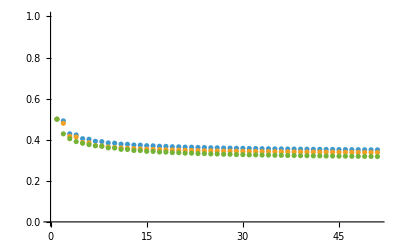

```mathematica
ListPlot[DeficiencyPlot[adag**adag**adag+a**a**a,ⅈ,50],PlotRange->{0,1}]
```

The Raabe criterion also indicates convergence to finite values.

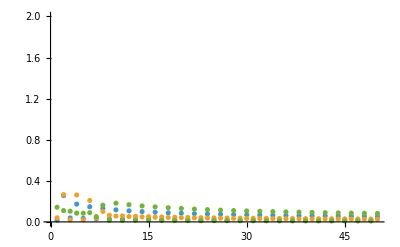

```mathematica
ListPlot[raabeList/@DeficiencyPlot[adag**adag**adag+a**a**a,ⅈ,50],PlotRange->{0,2}]
```